```mathematica
(* Doing Alard FS Decomp 
(see Alard 2008, eqs 4-5)
MSSG , MMakler; 
 Started Oct 5, 2010 
Current: Oct 12, 2010 *)
```

```mathematica
Remove["Global`*"] (* Clearing all vars *)
```

```mathematica
(* PE SIS model density function, from Keeton *)
phif[eps_]=ArcTan[Sqrt[(1+eps)/ (1-eps) ]Tan[v]];
rhot[v_,eps_] = (1 + eps Cos[2 phif[eps]])/Sqrt[(1-eps)(Cos[v])^2 + (1+eps)( Sin[v])^2  ]  ;
rho[u_,v_] = (1 + eps Cos[2 phin[eps]])/Sqrt[(1-eps)(u Cos[v])^2 + (1+eps)(u Sin[v])^2  ]  ;
```

```mathematica
(* Example plot *)
```

```mathematica
N[rhot[Pi/4,0.1]]
```

0.99

0.1

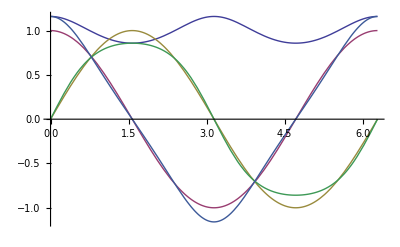

```mathematica
epss = 0.1
Plot[{ rhot[v,epss], Cos[v],Sin[v],rhot[v,epss]Sin[v],rhot[v,epss]Cos[v]},{v,0,2 Pi}]
```

```mathematica
(* Turn off num'l integration warnings *)
Off[NIntegrate::inumr]
Off[NIntegrate::ncvb]
```

```mathematica
(* Do num'l integrals over theta *)
ar [eps_,n_]= NIntegrate[rhot[v,eps] Cos[ n v] , {v,0, 2 Pi}]
br [eps_,n_]= NIntegrate[rhot[v,eps] Sin[ n v] , {v,0, 2 Pi}]
```

NIntegrate[rhot[v,eps] Cos[n v],{v,0,2 π}]

NIntegrate[rhot[v,eps] Sin[n v],{v,0,2 π}]

```mathematica
ar[0.1,2]
br[0.1,2]
```

0.471682

0.

```mathematica
(* Do analytic integrals over r *)
a[n_,eps_] = (1/(2 Pi n)) Integrate[(1/u) ar[eps,n] u^(n+1) , {u,0, 1}]
b[n_,eps_] = (1/(2 Pi n)) Integrate[(1/u) br[eps,n]u^(n+1) , {u,0, 1}]
c[n_,eps_] = (1/(2 Pi n)) Integrate[(1/u) ar[eps,n] u^(1-n) , {u,1, Infinity}]
d[n_,eps_] = (1/(2 Pi n)) Integrate[(1/u) br[eps,n] u^(1-n) , {u,1, Infinity}]
```

1/(2 n π)If[Re[n]>-1,1/(1+n),Integrate[u^n,{u,0,1},Assumptions→Re[n]≤-1]] NIntegrate[rhot[v,eps] Cos[n v],{v,0,2 π}]

1/(2 n π)If[Re[n]>-1,1/(1+n),Integrate[u^n,{u,0,1},Assumptions→Re[n]≤-1]] NIntegrate[rhot[v,eps] Sin[n v],{v,0,2 π}]

1/(2 n π)If[Re[n]>1,1/(-1+n),Integrate[u^-n,{u,1,∞},Assumptions→Re[n]≤1]] NIntegrate[rhot[v,eps] Cos[n v],{v,0,2 π}]

1/(2 n π)If[Re[n]>1,1/(-1+n),Integrate[u^-n,{u,1,∞},Assumptions→Re[n]≤1]] NIntegrate[rhot[v,eps] Sin[n v],{v,0,2 π}]

```mathematica
(* Actual outputs we'll use *)
epss = 0.999;

nn= 2;
ae = a[nn,epss];
b[nn,epss];
ce = c[nn,epss];
d[nn,epss];
2(ae-ce)  (* This should be close to    -eta/2, for small eta *)
2(ae+ce)           (* This should be close to eta, for small eta *)

nn= 4
ae4 = a[nn,epss];
b[nn,epss];
ce4 = c[nn,epss];
d[nn,epss];
2(ae4-ce4)  (* This should be close to    -eta/2, for small eta *)
2(ae4+ce4)           (* This should be close to eta, for small eta *)
```

-0.59825

1.1965

4

-0.0593103

0.237241

```mathematica
(* Construct the f functions from the coeffs above *)
f1 = 0+0+2(ae-ce) Cos[2 v] + 4(ae4-ce4) Cos[4v]
df0dt = 0+0+ 2( ae+ce) Sin[2 v]+4(ae4-ce4) Sin[4v]
```

-0.59825 Cos[2 v]-0.118621 Cos[4 v]

1.1965 Sin[2 v]-0.118621 Sin[4 v]